0.121731

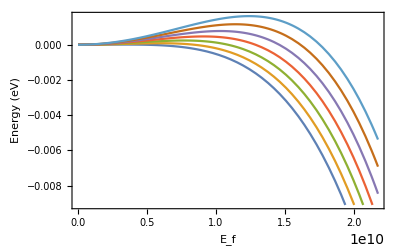

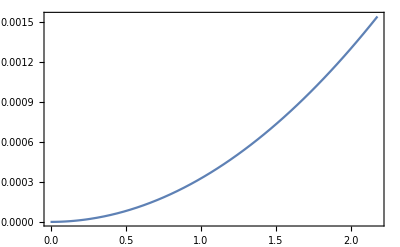

```mathematica
ℏ = 6.582*10^(-16); (*6.52*10^-16 [eV*s]*)
c = 2.998*10^8 ;(*2.998*10^8 [m/s]*)
q = 1.602*10^(-19);(*[C]*)
Subscript[m, e] = 0.51*10^6/c^2; (*0.51 [MeV/c^2]*)
m = 1*Subscript[m, e];
a = 0.56*10^(-9); (*[m]*)
(*a = 1*10^(-9);(*[m]*) *)
t = ℏ^2 / (2*m*a^2)
hw = 5*t;(*191 [mEv]*)
Efmax = 1*10^9; (*[V/m]*)
Efmax = 20*hw/a;
d = 1000*a;(*[m]*)
K = 2*π/d; (*[m^-1]*)

w[n_]:=(n+0.5)*(ℏ^2 * K / m )^2 * x^2 / hw^3 - (K*ℏ^3/hw^3)^2*x^4/(16*m^3) ;
Plot[{w[0],w[1],w[2],w[3],w[4],w[5], w[6]}, {x,0,Efmax}, Frame->True,FrameLabel->{"E_f", "Energy (eV)","",""}]
Plot[{w[1]-w[0]}, {x,0, Efmax}, Frame->True]
```